```mathematica
RHT={{0.065,1.0000968280312148}}
DHTOR={{0.065,0.00009739885978256312}}
MFVOR={{0.065,0.011120768670559306}}
FTDBZ={{0.065,3}}
```

{{0.065,1.0001}}

{{0.065,0.0000973989}}

{{0.065,0.0111208}}

{{0.065,3}}

```mathematica
zeta={{0.065,9105.84138582622}};
```

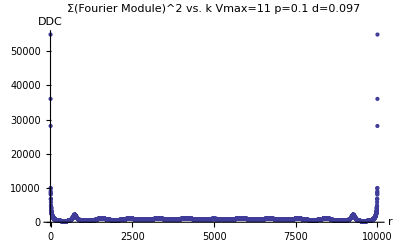

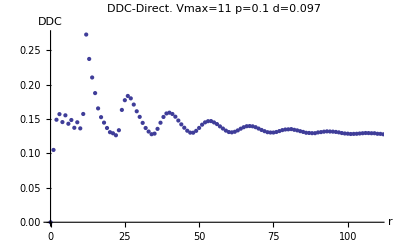

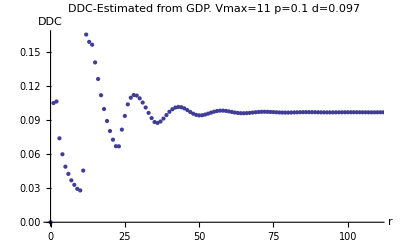

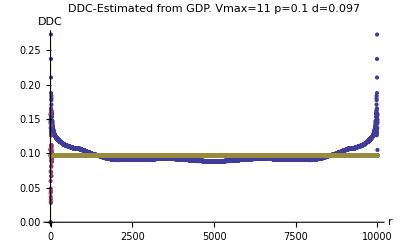

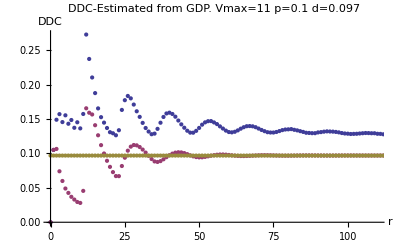

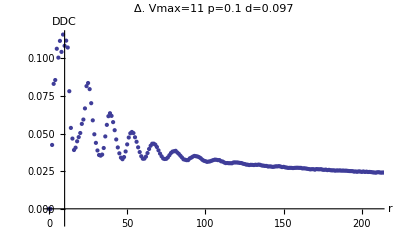

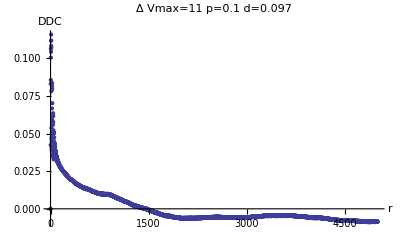

10000. = L

970 = N

0.0969097 = (N-1)/(L-1)

484.5 = (N-1)/2

484.456  : Sum of DDC-Half Track

484.651  : Sum of OZ-Half Track

-0.195362  : Sum of Δ

0.090029  : DDC-Averaged around L/2

0.0987636  : OZ-Averaged around L/2

1.09702  : Ratio at Half Track

0.0901316  : Δ at half track over random value

0.594562 = Mean of first 5*vmax values/Random Mean of DDC

1441  : First time Δ becomes 0

-0.0884397  = f

0.91156  =f1

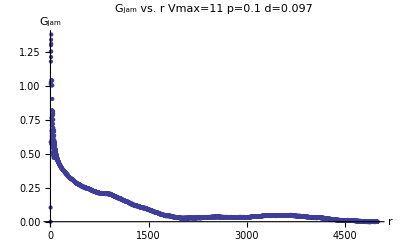

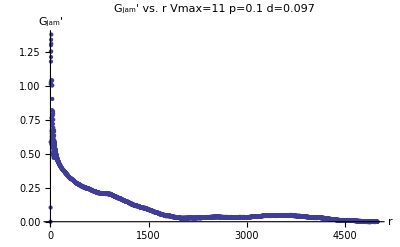

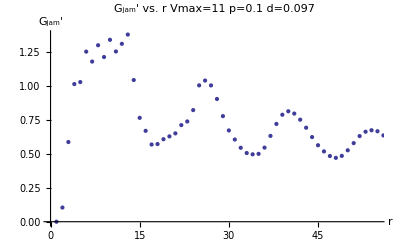

482.442

518863.  = ζ

1075.49  = ζ_2

1.

```mathematica
d="0.097";
p="0.1";
vmax="11";
n=10000.000;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*n];
prand=(m-1)/(n-1);
random=Table[{i,prand},{i,0,n}];
m2=(m-1)/2.;  
fourier="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/fine/fourier.1d.averaged.d";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/fine/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/fine/ddensitycorrelation.d";
g=".p"<>p<>".v11.txt";
fourieradd=fourier<>d<>g;
ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
Fou=ReadList[fourieradd,{Number,Number}];
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
ListPlot[Fou,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDCC,random},PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
ListPlot[{DDC,DDCC,random},PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
DDC2=DDC[[All,2]];
DDCC2=DDCC[[All,2]];
dif=Table[{i-1,DDC2[[i]]-DDCC2[[i]]},{i,1,n/2+1}];
dif2=dif[[All,2]];
ListPlot[dif,PlotLabel->"Δ.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{1,210},Full}]
ListPlot[dif,PlotLabel->"Δ  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
n "= L"
m  "= N  "
prand  "= (N-1)/(L-1)"
m2 "= (N-1)/2"
Sum[DDC2[[i]],{i,1,n/2}] " : Sum of DDC-Half Track"
Sum[DDCC2[[i]],{i,1,n/2}]  " : Sum of OZ-Half Track"
Sum[dif2[[i]],{i,1,n/2}]  " : Sum of Δ"
DDCF=Sum[DDC2[[i]],{i,n/2-5*11,n/2}]/(5*11);
DDCF  " : DDC-Averaged around L/2"
DDCCF=Sum[DDCC2[[i]],{i,n/2-5*11,n/2}]/(5*11);
DDCCF " : OZ-Averaged around L/2"
DDCCF/DDCF " : Ratio at Half Track"
(DDCCF-DDCF)/prand  " : Δ at half track over random value"
diff=Table[{i,(DDC2[[i]]-DDCC2[[i]])},{i,0,n/2}];
diff2=diff[[All,2]];
sum=Sum[Abs[diff2[[i]]],{i,1,55}]/(55);
sum/prand  "= Mean of first 5*vmax values/Random Mean of DDC"
x=3; While[dif2[[x]]>0.00005,x++]
x " : First time Δ becomes 0"

f=(DDCF-DDCCF)/DDCCF;
f1=DDCF/DDCCF;
f " = f"
f1 " =f1"
GJAM=Table[{i,(DDC2[[i]]-(1+f)*DDCC2[[i]])/(-f)},{i,1,n/2}];
GJAMp=Table[{i,(DDC2[[i]]-f1*DDCC2[[i]])/(1-f1)},{i,1,n/2}];
GJAM2=GJAM[[All,2]];
GJAMp2=GJAMp[[All,2]];
ListPlot[GJAM,PlotLabel->"G_jam vs. r  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"G_jam"},PlotRange->Full]
ListPlot[GJAMp,PlotLabel->"G_jam'  vs. r  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"G_jam'"},PlotRange->Full]
ListPlot[GJAMp,PlotLabel->"G_jam'  vs. r  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"G_jam'"},PlotRange->{{0,55},Full}]
ζ=Sum[i*GJAM2[[i]],{i,1,n/2}];
ζ2=Sum[i*GJAMp2[[i]],{i,1,n/2}];
SumGjam=Sum[GJAM2[[i]],{i,1,n/2}]
ζ " = ζ"
ζ2 /=SumGjam;
ζ2 " = ζ_2"
-f+f1
zeta=Append[zeta,{o,ζ2}];
```

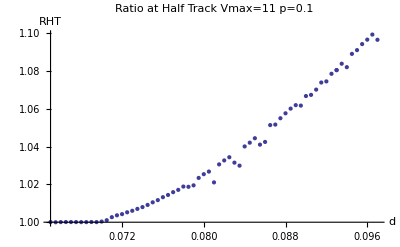

ListPlot[DHTOR,PlotLabel→Δ at half track over random value  Vmax=11  p=0.1,AxesLabel→{d,Δ},PlotRange→Full]

ListPlot[MFVOR,PlotLabel→Mean of first 5*vmax values/Random Mean of DDC11  p=0.1,AxesLabel→{d,Δ/Rnd},PlotRange→Full]

ListPlot[FTDBZ,PlotLabel→First time Δ becomes zero11  p=0.1,AxesLabel→{d,X},PlotRange→Full]

-0.000104643  = f

0.999895  =f1

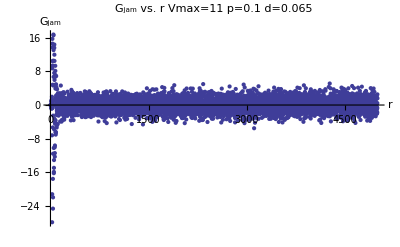

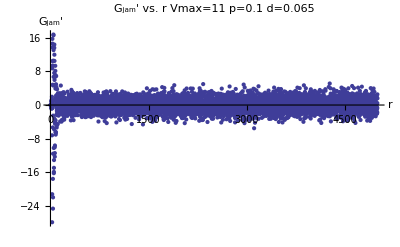

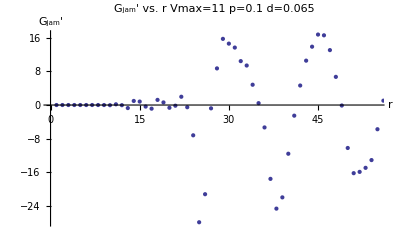

48.1059

438045.  = ζ

9105.84  = ζ_2

1.

```mathematica
ListPlot[RHT,PlotLabel->"Ratio at Half Track  Vmax="<>vmax<>"  p="<>p,AxesLabel->{"d","RHT"},PlotRange->Full]
ListPlot[DHTOR,PlotLabel->"Δ at half track over random value  Vmax="<>vmax<>"  p="<>p,AxesLabel->{"d","Δ"},PlotRange->Full]
ListPlot[MFVOR ,PlotLabel->"Mean of first 5*vmax values/Random Mean of DDC"<>vmax<>"  p="<>p,AxesLabel->{"d","Δ/Rnd"},PlotRange->Full]
ListPlot[FTDBZ,PlotLabel->"First time Δ becomes zero"<>vmax<>"  p="<>p,AxesLabel->{"d","X"},PlotRange->Full]
```

-Graphics-

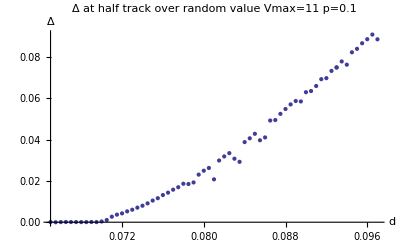

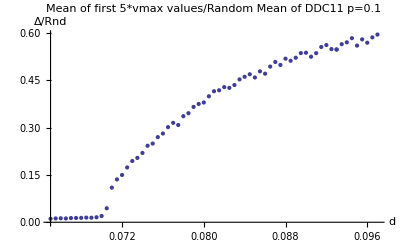

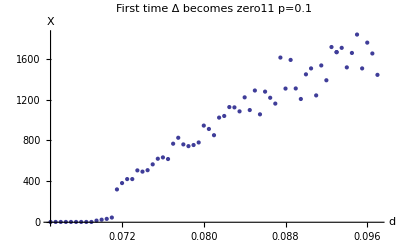

```mathematica
RHT=Append[RHT,{o,DDCCF/DDCF}];
DHTOR=Append[DHTOR,{o,(DDCCF-DDCF)/prand }];
MFVOR=Append[MFVOR,{o,sum/prand}];
FTDBZ=Append[FTDBZ,{o,x}];
```

```mathematica
RHT
DHTOR
MFVOR
FTDBZ
```

```mathematica
RHT={{0.065,1.0000968280312148},{0.0655,0.9999817902525039},{0.066,1.000064785494027},{0.0665,1.0000997820100228},{0.067,1.0000879120974144},{0.0675,1.0000754070600255},{0.068,1.0000510207025235},{0.0685,1.0000510314378455},{0.069,1.0001163227956056},{0.0695,1.000063118017289},{0.07,1.0003523801073173},{0.0705,1.0010588202450583},{0.071,1.0026696278532001},{0.0715,1.0036540782854535},{0.072,1.0042798846494372},{0.0725,1.0052526482078354},{0.073,1.0060602266826533},{0.0735,1.0070661841775856},{0.074,1.0080056692891672},{0.0745,1.0091538457842057},{0.075,1.0105307423906273},{0.0755,1.0116993812611388},{0.076,1.0132557757102494},{0.0765,1.0144369136495044},{0.077,1.015913023517215},{0.0775,1.0171362893739855},{0.078,1.0188815393695867},{0.0785,1.0187491178396608},{0.079,1.0195229982466858},{0.0795,1.023458624680497},{0.08,1.02543760970493},{0.0805,1.0268184038826096},{0.081,1.021090798427233},{0.0815,1.030631891590811},{0.082,1.0327244282512327},{0.0825,1.0344093306563973},{0.083,1.0315522378323174},{0.0835,1.0299593051237712},{0.084,1.0401316626045707},{0.0845,1.042121967807752},{0.085,1.0444716571120323},{0.0855,1.04108437228086},{0.086,1.0425171469551822},{0.0865,1.051438888605139},{0.087,1.0516951228225302},{0.0875,1.0550588956927272},{0.088,1.0576707368970606},{0.0885,1.0601514661764406},{0.089,1.0619925359996245},{0.0895,1.061757927255278},{0.09,1.0668108161036218},{0.0905,1.0674334831710939},{0.0915,1.0739822425588366},{0.091,1.0702202868937523},{0.092,1.0745686537298946},{0.0925,1.0786030502076438},{0.093,1.0805451827552415},{0.093,1.0805451827552415},{0.0935,1.0839387398855822},{0.094,1.0821091042989581},{0.0945,1.0891421422724255},{0.095,1.0911320334516386},{0.0955,1.094329519435995},{0.096,1.0966809439197402},{0.0965,1.0993766825723896},{0.097,1.0966123737224305}}
```

{{0.065,1.0001},{0.0655,0.999982},{0.066,1.00006},{0.0665,1.0001},{0.067,1.00009},{0.0675,1.00008},{0.068,1.00005},{0.0685,1.00005},{0.069,1.00012},{0.0695,1.00006},{0.07,1.00035},{0.0705,1.00106},{0.071,1.00267},{0.0715,1.00365},{0.072,1.00428},{0.0725,1.00525},{0.073,1.00606},{0.0735,1.00707},{0.074,1.00801},{0.0745,1.00915},{0.075,1.01053},{0.0755,1.0117},{0.076,1.01326},{0.0765,1.01444},{0.077,1.01591},{0.0775,1.01714},{0.078,1.01888},{0.0785,1.01875},{0.079,1.01952},{0.0795,1.02346},{0.08,1.02544},{0.0805,1.02682},{0.081,1.02109},{0.0815,1.03063},{0.082,1.03272},{0.0825,1.03441},{0.083,1.03155},{0.0835,1.02996},{0.084,1.04013},{0.0845,1.04212},{0.085,1.04447},{0.0855,1.04108},{0.086,1.04252},{0.0865,1.05144},{0.087,1.0517},{0.0875,1.05506},{0.088,1.05767},{0.0885,1.06015},{0.089,1.06199},{0.0895,1.06176},{0.09,1.06681},{0.0905,1.06743},{0.0915,1.07398},{0.091,1.07022},{0.092,1.07457},{0.0925,1.0786},{0.093,1.08055},{0.093,1.08055},{0.0935,1.08394},{0.094,1.08211},{0.0945,1.08914},{0.095,1.09113},{0.0955,1.09433},{0.096,1.09668},{0.0965,1.09938},{0.097,1.09661}}

```mathematica
DHTOR={{0.065,0.00009739885978256312},{0.0655,-0.000018318990823529837},{0.066,0.00006516798938228809},{0.0665,0.0001003664683693583},{0.067,0.00008842708520389904},{0.0675,0.00007584890208192279},{0.068,0.00005132034609389537},{0.0685,0.000051330592107772004},{0.069,0.00011699582003425572},{0.0695,0.00006348592218648692},{0.07,0.000354327939916848},{0.0705,0.0010654242887562619},{0.071,0.002681909491523038},{0.0715,0.0036672157994425618},{0.072,0.0042865418428319904},{0.0725,0.005255677292815416},{0.073,0.0060587967283991075},{0.0735,0.007057394264300204},{0.074,0.007988184986467306},{0.0745,0.00912337887096954},{0.075,0.01048129792389405},{0.0755,0.011630896114058526},{0.076,0.013157822905139956},{0.0765,0.014313424535336123},{0.077,0.015753850630690777},{0.0775,0.016944335465119136},{0.078,0.01863790145699264},{0.0785,0.018509442933672217},{0.079,0.01925864543726607},{0.0795,0.023051810686395148},{0.08,0.024948039705880606},{0.0805,0.0262666855970186},{0.081,0.02077262193448407},{0.0815,0.029890253918918332},{0.082,0.03186718703297137},{0.0825,0.033453125006063754},{0.083,0.030760165259348365},{0.0835,0.029252181312955115},{0.084,0.03880094669248743},{0.0845,0.04064718972156264},{0.085,0.04281777047703775},{0.0855,0.039684885702573884},{0.086,0.04105993258741186},{0.0865,0.049253717346463395},{0.087,0.049486347476956336},{0.0875,0.05247755284324838},{0.088,0.05483084897610756},{0.0885,0.057055230763573585},{0.089,0.058699222035995285},{0.0895,0.058489630419462056},{0.09,0.06297502454949784},{0.0905,0.06352447455198892},{0.0915,0.06926780894967065},{0.091,0.06597708000000045},{0.092,0.06977833653427443},{0.0925,0.07327801188311699},{0.093,0.07495317523143183},{0.093,0.07495317523143183},{0.0935,0.07786613221091938},{0.094,0.07629721509584833},{0.0945,0.08229709015360201},{0.095,0.08398027820863989},{0.0955,0.08667236867924676},{0.096,0.08864196437956277},{0.0965,0.0908896464522818},{0.097,0.08858368226006437}}
```

```mathematica
MFVOR={{0.065,0.011120768670559306},{0.0655,0.012090616523742959},{0.066,0.012588224452465529},{0.0665,0.012009834170591977},{0.067,0.013328859312828279},{0.0675,0.013519094019274654},{0.068,0.013924674083838382},{0.0685,0.014693251909573685},{0.069,0.014350125950367776},{0.0695,0.015750012085391375},{0.07,0.01982753707475243},{0.0705,0.04417394076910521},{0.071,0.10963464732998449},{0.0715,0.13575063040397645},{0.072,0.1497702104360167},{0.0725,0.17354527467959785},{0.073,0.1939368031682743},{0.0735,0.20382868185502812},{0.074,0.21946032664426085},{0.0745,0.24239948762563165},{0.075,0.24931284446387994},{0.0755,0.26966294921283346},{0.076,0.28103723472956976},{0.0765,0.30127399975531244},{0.077,0.3148936417399569},{0.0775,0.30802333947021665},{0.078,0.3359821609966427},{0.0785,0.3454181322105918},{0.079,0.36538241729701065},{0.0795,0.37475048987324755},{0.08,0.37929573784120785},{0.0805,0.3990409848486143},{0.081,0.41502165655817036},{0.0815,0.4180773305877814},{0.082,0.42801005683810767},{0.0825,0.4256835313774057},{0.083,0.43484150158525514},{0.0835,0.45247668117994155},{0.084,0.46077836502672304},{0.0845,0.4686824046484768},{0.085,0.45857326725446734},{0.0855,0.4780600470356207},{0.086,0.47061096482029},{0.0865,0.49309207797874893},{0.087,0.5076474346539765},{0.0875,0.4982826613863363},{0.088,0.5181457003920334},{0.0885,0.5115158536664622},{0.089,0.521105203196198},{0.0895,0.5358069260246721},{0.09,0.5369311343612904},{0.0905,0.5243499579858211},{0.0915,0.5551620261966473},{0.091,0.5356216890549398},{0.092,0.5612770378347297},{0.0925,0.5485637337773962},{0.093,0.5471352647237141},{0.093,0.5471352647237141},{0.0935,0.5641322380523928},{0.094,0.5699328186974458},{0.0945,0.583060316674338},{0.095,0.5596219952673014},{0.0955,0.5793219980655896},{0.096,0.5686432388462},{0.0965,0.585581802488451},{0.097,0.594561593388906}}
```

```mathematica
FTDBZ={{0.065,3},{0.0655,3},{0.066,3},{0.0665,3},{0.067,3},{0.0675,3},{0.068,3},{0.0685,3},{0.069,3},{0.0695,16},{0.07,25},{0.0705,33},{0.071,46},{0.0715,321},{0.072,383},{0.0725,422},{0.073,422},{0.0735,507},{0.074,495},{0.0745,509},{0.075,566},{0.0755,621},{0.076,634},{0.0765,618},{0.077,768},{0.0775,826},{0.078,761},{0.0785,744},{0.079,755},{0.0795,780},{0.08,945},{0.0805,912},{0.081,851},{0.0815,1023},{0.082,1039},{0.0825,1126},{0.083,1123},{0.0835,1084},{0.084,1221},{0.0845,1097},{0.085,1288},{0.0855,1055},{0.086,1277},{0.0865,1217},{0.087,1160},{0.0875,1610},{0.088,1307},{0.0885,1587},{0.089,1308},{0.0895,1205},{0.09,1446},{0.0905,1504},{0.0915,1533},{0.091,1240},{0.092,1388},{0.0925,1713},{0.093,1663},{0.093,1663},{0.0935,1705},{0.094,1514},{0.0945,1655},{0.095,1835},{0.0955,1504},{0.096,1756},{0.0965,1650},{0.097,1441}}
```

```mathematica
RHT2=RHT[[All,2]];
RHT1=RHT[[All,1]];
```

```mathematica
RHT51=Table[{RHT1[[i]],1-1/RHT2[[i]]},{i,1,Length[RHT1]}];
```

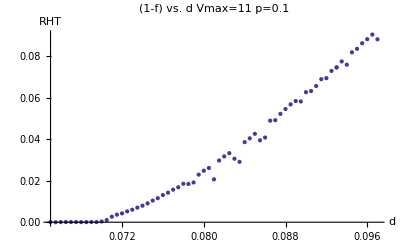

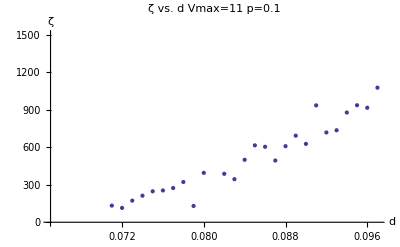

```mathematica
ListPlot[RHT51,PlotLabel->"(1-f) vs. d  Vmax="<>vmax<>"  p="<>p,AxesLabel->{"d","RHT"},PlotRange->{{0.065,0.097},Full}]
ListPlot[zeta,PlotLabel->"ζ vs. d  Vmax="<>vmax<>"  p="<>p,AxesLabel->{"d","ζ"},PlotRange->{{0.065,0.097},{0,1500}}]
```

```mathematica
zeta
```

{{0.065,9105.84},{0.066,5706.17},{0.067,2698.27},{0.068,3623.55},{0.069,2271.8},{0.07,-3023.14},{0.071,133.075},{0.072,114.612},{0.073,172.753},{0.074,212.226},{0.075,247.385},{0.076,254.096},{0.077,273.411},{0.078,321.774},{0.079,130.227},{0.08,394.78},{0.081,-388.304},{0.082,387.127},{0.083,344.121},{0.084,499.075},{0.085,614.612},{0.086,603.101},{0.087,493.227},{0.088,608.003},{0.089,691.925},{0.09,626.376},{0.091,934.071},{0.092,717.493},{0.093,735.049},{0.094,876.806},{0.095,935.135},{0.096,915.156},{0.097,1075.49}}